```mathematica
$ProcessorCount
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

8

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

```mathematica
Needs["CCompilerDriver`GenericCCompiler`"]
$CCompiler={"Compiler"->GenericCCompiler,"CompilerInstallation"->"E:\\mingw-w64\\x86_64-8.1.0-posix-seh-rt_v6-rev0\\mingw64","CompilerName"->"x86_64-w64-mingw32-gcc.exe"};
<<CompiledFunctionTools`(*позволяет смотреть "код"*)
```

```mathematica
Nc=40;(*число периодов спиральной среды*)
qc=1;(*волновой вектор холестерика в эВ*)
Lz=2 Pi/qc Nc ;(*толщина пластины холестерика в 1/эВ*)
lev=1.24;(*длина волны фотона энергии 1 эВ в мкм. lev/(2 Pi) -- единица длины*)
mMax =10;(*ожидаемое максимальное значение m*)
```

```mathematica
ϵpp=Compile[{{k0,_Real}},2.4
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*перпендикулярная диэлектрическая проницаемость. ϵ3*)
ϵav=Compile[{{k0,_Real}},Evaluate[(2.4+2.9)/2]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*средняя диэлектрическая проницаемость. ϵ*)
Ah=Compile[{{k0,_Real}},Evaluate[(2.9-2.4)/4]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];
Ahc=Compile[{{k0,_Real}},Evaluate[Conjugate[(2.9-2.4)/4]]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];
(*комплексная анизотропия. A*)
αh=Compile[{{k0,_Real}},1/10
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];
αhc=Compile[{{k0,_Real}},Evaluate[Conjugate[1/10]]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*комплексная биаксиальность. α*)
βh=Compile[{{k0,_Real}},1/20
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];
βhc=Compile[{{k0,_Real}},Evaluate[Conjugate[1/20]]
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*комплексная биаксиальность. β*)
yh=Compile[{{k0,_Real}},1/100
,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"](*гиротропность. y*);
ϵvac=ϵav[qc];(*диэлектрическая проницаемость окружающей среды*)
Print["Волновой вектор спиральной среды q: ",qc, " эВ"]
Print["Толщина пластины из спиральной среды Lz: ",Lz lev/(2 Pi), " мкм"]
Module[{xx=qc},(*предполагаемая энергия фотона*)
Print["Показатели преломления: n_3=",Sqrt[ϵpp[xx]], ", n_ave=",Sqrt[ϵav[xx]],", n_vac=",Sqrt[ϵvac]]]
```

Волновой вектор спиральной среды q: 1 эВ

Толщина пластины из спиральной среды Lz: 49.6 мкм

Показатели преломления: n_3=1.54919, n_ave=1.62788, n_vac=1.62788

```mathematica
(*risse2018: no=1.5; ne=1.8; nvac=1.4688*)
```

```mathematica
pp=3;(*2p+1-волновое приближение*)
```

```mathematica
Block[{qn,kp,k3bs,k0s,a,b,ac,bc,A,Ac,ep,y},
Module[{U0,U1,bcV1,bsVb,k0sV0,eqs,ceq1,ceq2,t,eh1,eh2,ap,am,p3},
U0={{1+kp^2/2/k3bs,kp^2/2/k3bs},{kp^2/2/k3bs,1+kp^2/2/k3bs}};
U1=2 {{bc t+b/t,(ac+bc) t},{(a+b)/t,a/t+ac t}};
bcV1=2 {{b/t,-ac t},{b/t,-ac t}};
bsVb=4 {{b bc,ac bc t^2},{a b/t^2,a ac}};
k0sV0={{(ep-y) k0s-kp^2/2,kp^2/2+Ac k0s t^2},{kp^2/2+A k0s/t^2,(ep+y) k0s-kp^2/2}};

eqs=(-p3^2 U0-kp k0s/(2 k3bs) p3 U1+k0sV0+k0s kp/(2 k3bs) bcV1-k0s^2/(2 k3bs) bsVb).{ap[p3],am[p3]};

ceq1=CoefficientList[t^2 eqs[[1]],t];
ceq2=CoefficientList[t^2 eqs[[2]],t];

eh1[n_]:=Collect[Total[MapIndexed[(#1/.(p3->p3-(First[#2]-3)))&,ceq1]],{ap[_],am[_]},FullSimplify]/.{p3->qn+n};
eh2[n_]:=Collect[Total[MapIndexed[(#1/.(p3->p3-(First[#2]-3)))&,ceq2]],{ap[_],am[_]},FullSimplify]/.{p3->qn+n-2};
MMV[p_]:=Module[{Polys,Elems},
Polys={};
Elems={};
Do[
AppendTo[Polys,eh1[-i]==0];
AppendTo[Polys,eh2[-i]==0];
AppendTo[Elems,ap[-i+qn]];
AppendTo[Elems,am[-i+qn-2]];
,{i,-p,p}];

CoefficientArrays[Polys,Elems][[2]]//Normal
]
]]
```

```mathematica
Block[{qn,kp,k3bs,k0s,a,b,ac,bc,A,Ac,ep,y},mmi[p_]:=Drop[Drop[MMV[p],-1,-1],1,1]]
```

```mathematica
Block[{qn,kp,k3bs,k0s,a,b,ac,bc,A,Ac,ep,y},
If[FailureQ[FindFile[NotebookDirectory[]<>"DisperHelDet"<>ToString[pp]<>".dat"]]==True,
dspp=If[pp≤5,
Module[{ii,cl,cll,det},
det=Det[mmi[pp]];
cl=CoefficientList[det,qn];
cll=Length[cl];
cl=ParallelMap[Simplify,cl,Method->"FinestGrained"];
det=0;
Do[det+=cl[[ii]] qn^(ii-1),{ii,1,cll}];
det]
,Collect[Det[mmi[pp]],qn]];(*дисперсионнный определитель. если есть, то загружается из файла*)
Put[dspp,NotebookDirectory[]<>"DisperHelDet"<>ToString[pp]<>".dat"];,
dspp=Get[NotebookDirectory[]<>"DisperHelDet"<>ToString[pp]<>".dat"];];

mmieq=mmi[pp];  (*матрица уравнения*) 
]
```

```mathematica
Block[{qn,kp,k3bs,k0s,a,b,ac,bc,A,Ac,ep,y},
dsp[k0s1_?NumberQ,kp1_?NumberQ,k3bs1_?NumberQ,Aa1_?NumberQ,Aa1c_?NumberQ,a1_?NumberQ,a1c_?NumberQ,b1_?NumberQ,b1c_?NumberQ,y1_?NumberQ,ep1_?NumberQ,qn1_]=dspp/.{k0s->k0s1,kp->kp1,k3bs->k3bs1,qn->qn1,A->Aa1,Ac->Aa1c,a->a1,ac->a1c,b->b1,bc->b1c,y->y1,ep->ep1};
meq=Compile[{{k0s1,_Real},{kp1,_Real},{k3bs1,_Real},{Aa1,_Complex},{Aa1c,_Complex},{a1,_Complex},{a1c,_Complex},{b1,_Complex},{b1c,_Complex},{y1,_Real},{ep1,_Real},{qn1,_Complex}},Evaluate[mmieq/.{k0s->k0s1,kp->kp1,k3bs->k3bs1,qn->qn1,A->Aa1,Ac->Aa1c,a->a1,ac->a1c,b->b1,bc->b1c,y->y1,ep->ep1}]
,RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*функции для определителя и матрицы*)
]
```

```mathematica
Block[{qn,kp,k3bs,k0s,a,b,ac,bc,A,Ac,ep,y},PolynomialQ[dspp,qn]]
```

True

```mathematica
ChoiceMainBranch=Compile[{{p,_Integer},{k0s,_Real},{kp,_Real},{k3bs,_Real},{Aa,_Complex},{Aac,_Complex},{a,_Complex},{ac,_Complex},{b,_Complex},{bc,_Complex},{y,_Real},{ϵ,_Real},{rts,_Complex,1}},Module[{i,j,k,nmax,ff,rtss,mm1,mm1n,eigv,eigv1,eigvr,partnorm,nv1,crit=0.5},
Do[
rtss=rts[[i]];
mm1n=meq[k0s,kp,k3bs,Aa,Aac,a,ac,b,bc,y,ϵ,rtss];
eigv=NullSpace[mm1n];
Do[
eigv1=eigv[[k]];
nv1=Norm[eigv[[k]]];
eigv1=eigv1/nv1;
partnorm=Abs[eigv1[[2 p]]]^2+Abs[eigv1[[2 p+1]]]^2+Abs[eigv1[[2 p-3]]]^2;(*+Abs[eigv1[[2 p-1]]]^2*)
If[partnorm<crit,,
eigvr=Append[eigv1,rtss];
Sow[eigvr];](*записываем в стек (СВ,СЗ), СЗ -- последний элемент с номером 4p+1*);
,{k,1,Length[eigv]}];
,{i,1,Length[rts]}];
],{{NullSpace[_],_Complex,2},{Length[_],_Integer},{Norm[_],_Real},{meq[_,_,_,_,_,_,_,_,_,_,_],_Complex,2},{Sow[_],_Complex,1}},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];

Branches[p_?NumberQ,k0s_?NumberQ,kp_?NumberQ,k3bs_?NumberQ,Aa_?NumberQ,Aac_?NumberQ,a_?NumberQ,ac_?NumberQ,b_?NumberQ,bc_?NumberQ,y_?NumberQ,ϵ_?NumberQ]:=Module[{rts,ddsp,q1,bb},
ddsp=dsp[k0s,kp,k3bs,Aa,Aac,a,ac,b,bc,y,ϵ,q1];
rts=q1/.{ToRules[NRoots[ddsp==0,q1,PrecisionGoal->30]]};
bb=Reap[ChoiceMainBranch[p,k0s,kp,k3bs,Aa,Aac,a,ac,b,bc,y,ϵ,rts]];
Last[bb][[1]]];
```

```mathematica
SetSharedFunction[ParallelSow]
ParallelSow[ex_]:=Sow[ex];
```

```mathematica
With[{qc=qc},
DisperMain[p_?IntegerQ,kp_?NumberQ,k3bs_?NumberQ,Aa_?NumberQ,Aac_?NumberQ,a_?NumberQ,ac_?NumberQ,b_?NumberQ,bc_?NumberQ,y_?NumberQ,ϵ_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k00,k0,k0ie,k0fe,dk0e,kpe,k3bse,Aae,Aace,ae,ace,be,bce,ye,ϵe},
k0ie=SetPrecision[k0i,Infinity];
k0fe=SetPrecision[k0f,Infinity];
dk0e=SetPrecision[dk0,Infinity];
kpe=SetPrecision[kp,Infinity];
k00=k0 qc;
k3bse=SetPrecision[ϵpp[k00] k0^2-kp^2,Infinity];
Aae=SetPrecision[Aa,Infinity];(*точные числа*)
Aace=SetPrecision[Aac,Infinity];
ae=SetPrecision[a,Infinity];
ace=SetPrecision[ac,Infinity];
be=SetPrecision[b,Infinity];
bce=SetPrecision[bc,Infinity];
ye=SetPrecision[y,Infinity];
ϵe=SetPrecision[ϵ,Infinity];

Last[Reap[
ParallelDo[Module[{llb,i},
llb=Branches[p,k0^2,kpe,k3bse,Aae,Aace,ae,ace,be,bce,ye,ϵe];
Do[ParallelSow[{llb[[i,4 p+1]],k0}],{i,1,Length[llb]}]]
,{k0,k0ie,k0fe,dk0e}]]][[1]]];]

With[{qc=qc},
DisperMainK00np[p_?IntegerQ,np1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k0,k0ie,k0fe,dk0e,npe},
k0ie=SetPrecision[k0i,Infinity];
k0fe=SetPrecision[k0f,Infinity];
dk0e=SetPrecision[dk0,Infinity];
npe=SetPrecision[np1,Infinity];(*точные числа*)

Last[Reap[
ParallelDo[Module[{llb,i,k0s,k00,kpe,Aae,Aace,ae,ace,be,bce,ye,ϵe,k3bse},
k00=k0 qc;
Aae=SetPrecision[Ah[k00],Infinity];
Aace=SetPrecision[Ahc[k00],Infinity];
ae=SetPrecision[αh[k00],Infinity];
ace=SetPrecision[αhc[k00],Infinity];
be=SetPrecision[βh[k00],Infinity];
bce=SetPrecision[βhc[k00],Infinity];
ye=SetPrecision[yh[k00],Infinity];
ϵe=SetPrecision[ϵav[k00],Infinity];
kpe=k0 npe;
k3bse=SetPrecision[ϵpp[k00] k0^2-kpe^2,Infinity];
llb=Branches[p,k0^2,kpe,k3bse,Aae,Aace,ae,ace,be,bce,ye,ϵe];
Do[ParallelSow[{llb[[i,4 p+1]],k0}],{i,1,Length[llb]}]]
,{k0,k0ie,k0fe,dk0e}]]][[1]]];]
```

```mathematica
With[{qc=qc},
DisperSimpl[kp1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k0,k0ie,k0fe,dk0e,kpe,dee},
k0ie=SetPrecision[k0i,Infinity];
k0fe=SetPrecision[k0f,Infinity];
dk0e=SetPrecision[dk0,Infinity];
kpe=SetPrecision[kp1,Infinity];(*точные числа*)

Last[Reap[
ParallelDo[Module[{rts1,rts2,i,dssp,q1,k00,Aae,Aace,ae,ace,be,bce,ye,ϵe,k3bse},
k00=k0 qc;
Aae=SetPrecision[Ah[k00],Infinity];
Aace=SetPrecision[Ahc[k00],Infinity];
ae=SetPrecision[αh[k00],Infinity];
ace=SetPrecision[αhc[k00],Infinity];
be=SetPrecision[βh[k00],Infinity];
bce=SetPrecision[βhc[k00],Infinity];
ye=SetPrecision[yh[k00],Infinity];
ϵe=SetPrecision[ϵav[k00],Infinity];
k3bse=SetPrecision[ϵpp[k00] k0^2-kp1^2,Infinity];

dssp=dsp[k0^2,kpe,k3bse,Aae,Aace,ae,ace,be,bce,ye,ϵe,q1];
rts1=q1/.{ToRules[NRoots[dssp==0,q1,PrecisionGoal->30]]};
rts2=Sort[Select[rts1,(Chop[#]∈Reals)&]];(*оставляем только вещественные корни*)
Do[ParallelSow[{Re[rts2[[i]]],k0}],{i,1,Length[rts2]}]]
,{k0,k0ie,k0fe,dk0e}]]][[1]]];]
```

```mathematica
(*vvvvvvvv+аналитический расчёт блоков матриц, входящих в уравнения сшивки+vvvvvvvvv*)
```

```mathematica
h0l={{((-sϵvac+n3) t0l)/(√2),((sϵvac+n3) t0l)/(√2),(-sϵvac-n3)/(√2 t0l),(sϵvac-n3)/(√2 t0l)},{((sϵvac+n3) t0l)/(√2),((-sϵvac+n3) t0l)/(√2),(sϵvac-n3)/(√2 t0l),(-sϵvac-n3)/(√2 t0l)},{(k0 (ϵvac-sϵvac n3) t0l)/(√2),(k0 (ϵvac+sϵvac n3) t0l)/(√2),(k0 (ϵvac+sϵvac n3))/(√2 t0l),(k0 (ϵvac-sϵvac n3))/(√2 t0l)},{(k0 (ϵvac+sϵvac n3) t0l)/(√2),(k0 (ϵvac-sϵvac n3) t0l)/(√2),(k0 (ϵvac-sϵvac n3))/(√2 t0l),(k0 (ϵvac+sϵvac n3))/(√2 t0l)}};
Gm={{(n3-sϵvac)/(√2),(n3+sϵvac)/(√2)},{(n3+sϵvac)/(√2),(n3-sϵvac)/(√2)},{(k0 (ϵvac-sϵvac n3))/(√2),(k0 (ϵvac+sϵvac n3))/(√2)},{(k0 (sϵvac n3+ϵvac))/(√2),(k0 (-sϵvac n3+ϵvac))/(√2)}};
```

```mathematica
-PadRight[h0l[[All,3;;4]],{4,4}]
-PadLeft[Gm,{4,4}]
```

{{-(-n3-sϵvac)/(√2 t0l),-(-n3+sϵvac)/(√2 t0l),0,0},{-(-n3+sϵvac)/(√2 t0l),-(-n3-sϵvac)/(√2 t0l),0,0},{-(k0 (n3 sϵvac+ϵvac))/(√2 t0l),-(k0 (-n3 sϵvac+ϵvac))/(√2 t0l),0,0},{-(k0 (-n3 sϵvac+ϵvac))/(√2 t0l),-(k0 (n3 sϵvac+ϵvac))/(√2 t0l),0,0}}

{{0,0,-(n3-sϵvac)/(√2),-(n3+sϵvac)/(√2)},{0,0,-(n3+sϵvac)/(√2),-(n3-sϵvac)/(√2)},{0,0,-(k0 (-n3 sϵvac+ϵvac))/(√2),-(k0 (n3 sϵvac+ϵvac))/(√2)},{0,0,-(k0 (n3 sϵvac+ϵvac))/(√2),-(k0 (-n3 sϵvac+ϵvac))/(√2)}}

```mathematica
h0l[[All,1;;2]]
h0l[[All,1;;2]].{dp,dm}//FullSimplify
```

{{((n3-sϵvac) t0l)/(√2),((n3+sϵvac) t0l)/(√2)},{((n3+sϵvac) t0l)/(√2),((n3-sϵvac) t0l)/(√2)},{(k0 t0l (-n3 sϵvac+ϵvac))/(√2),(k0 t0l (n3 sϵvac+ϵvac))/(√2)},{(k0 t0l (n3 sϵvac+ϵvac))/(√2),(k0 t0l (-n3 sϵvac+ϵvac))/(√2)}}

{((dp (n3-sϵvac)+dm (n3+sϵvac)) t0l)/(√2),((dm (n3-sϵvac)+dp (n3+sϵvac)) t0l)/(√2),(k0 t0l ((dm-dp) n3 sϵvac+(dm+dp) ϵvac))/(√2),(k0 t0l (dm (-n3 sϵvac+ϵvac)+dp (n3 sϵvac+ϵvac)))/(√2)}

```mathematica
(*^^^^^^^^^^+аналитический расчёт блоков матриц, входящих в уравнения сшивки+^^^^^^^^^^^*)
```

```mathematica
ClearAll[ScCoeffLinComb]
```

```mathematica
With[{qc=qc,Lz=Lz,ϵvac=ϵvac,sϵvac=Evaluate[Sqrt[ϵvac]]},
ScCoeffLinComb=Compile[{{dp,_Complex},{dm,_Complex},{k00,_Real},{k0,_Real},{k0s,_Real},{kp,_Real},{npx,_Real},{npy,_Real},{n3,_Real},{k3bs,_Real},{ac,_Complex},{be,_Complex},{p,_Integer},{branchs,_Complex,2},{numb,_Integer}},Module[{ii,ϕ,rff,u0t,umLt,t0l,h0l20,Gm0,frterm,row1,row2,eqnmb,brt},

ϕ=Arg[npx+I npy];rff=Exp[I ϕ];
(*общие фазовые множители*)

u0t=Table[Module[{tf,pf,ap,am,mrap,ram,l},(*транспонированная матрица U(0)*)
pf=branchs[[ii,4 p+1]];(*импульс закона дисперсии*)
tf=Exp[-I pf ϕ];(*фазовые множители, зависящие от ветви*)
ap=0.+I 0.;
am=0.+I 0.;
mrap=0.+I 0.;
ram=0.+I 0.;
Do[Module[{apl,aml,aplp1,amlm1},
apl=branchs[[ii,2 (p-l)]];
aml=If[2 (p-l)>3,branchs[[ii,2 (p-l)-3]],0+I 0.];
aplp1=If[l==p-1,0.+I 0.,branchs[[ii,2 (p-l-1)]]];
amlm1=branchs[[ii,2 (p-l)-1]];
ap+=apl/rff^l;
am+=aml/rff^l;
mrap+=((apl+kp^2/(2 k3bs) (apl+aml)) (pf+l)+k0s kp/k3bs (be aplp1+ac amlm1))/rff^l;
ram+=((aml+kp^2/(2 k3bs) (apl+aml)) (pf+l)+k0s kp/k3bs (be aplp1+ac amlm1))/rff^l;]
,{l,-p,p-1}];
{tf ap,tf am,tf mrap,tf ram}]
,{ii,1,numb}];

umLt=Table[Module[{tfl},(*транспонированная матрица U(-L). предполагаем целое число периодов*)
tfl=Exp[-I branchs[[ii,4 p+1]] qc Lz];
tfl u0t[[ii]]]
,{ii,1,numb}];

t0l=Exp[-I k00 n3 Lz];

h0l20={{-(-n3-sϵvac)/(√2 t0l),-(-n3+sϵvac)/(√2 t0l),0,0},{-(-n3+sϵvac)/(√2 t0l),-(-n3-sϵvac)/(√2 t0l),0,0},{-(k0 (n3 sϵvac+ϵvac))/(√2 t0l),-(k0 (-n3 sϵvac+ϵvac))/(√2 t0l),0,0},{-(k0 (-n3 sϵvac+ϵvac))/(√2 t0l),-(k0 (n3 sϵvac+ϵvac))/(√2 t0l),0,0}};
Gm0={{0,0,-(n3-sϵvac)/(√2),-(n3+sϵvac)/(√2)},{0,0,-(n3+sϵvac)/(√2),-(n3-sϵvac)/(√2)},{0,0,-(k0 (-n3 sϵvac+ϵvac))/(√2),-(k0 (n3 sϵvac+ϵvac))/(√2)},{0,0,-(k0 (n3 sϵvac+ϵvac))/(√2),-(k0 (-n3 sϵvac+ϵvac))/(√2)}};

frterm={((dp (n3-sϵvac)+dm (n3+sϵvac)) t0l)/(√2),((dm (n3-sϵvac)+dp (n3+sϵvac)) t0l)/(√2),(k0 t0l ((dm-dp) n3 sϵvac+(dm+dp) ϵvac))/(√2),(k0 t0l (dm (-n3 sϵvac+ϵvac)+dp (n3 sϵvac+ϵvac)))/(√2),0,0,0,0};

row1=Join[Transpose[umLt],h0l20,2];
row2=Join[Transpose[u0t],Gm0,2];
eqnmb=Join[row1,row2];(*блочная матрица уравнения*)

brt=LinearSolve[eqnmb,frterm];

brt[[numb+1;;numb+4]]

],{{LinearSolve[_,_],_Complex,1}},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"]];
(*выдает ответ в виде списка (hp,hm,tp,tm). При желании можно выводить и ach.*)
```

```mathematica
CompilePrint[ScCoeffLinComb]
```

15 arguments
		1 Boolean register
		21 Integer registers
		47 Real registers
		26 Complex registers
		12 Tensor registers
		Underflow checking off
		Overflow checking off
		Integer overflow checking off
		RuntimeAttributes -> {}

		C0 = A1
		C1 = A2
		R0 = A3
		R1 = A4
		R2 = A5
		R3 = A6
		R4 = A7
		R5 = A8
		R6 = A9
		R7 = A10
		C2 = A11
		C3 = A12
		I0 = A13
		T(C2)0 = A14
		I1 = A15
		I18 = 0
		R18 = 2.65
		I5 = 4
		R15 = -1.6278820596099706
		C4 = 0. + 1. I
		R13 = 3.141592653589793
		I13 = 2
		C20 = 0. - 1. I
		I7 = -1
		I2 = 1
		I16 = 3
		R8 = 0.
		I17 = -3
		I20 = 80
		R14 = 1.6278820596099706
		Result = T(C1)11

1	C5 = R5 + R8 I
2	C6 = C4 * C5
3	C5 = R4 + R8 I
4	C5 = C5 + C6
5	R9 = Arg[ C5]
6	C5 = R9 + R8 I
7	C6 = C4 * C5
8	C5 = Exp[ C6]
9	I3 = I1
10	I4 = I7
11	T(C2)1 = Table[ I3, I4]
12	I8 = I18
13	goto 152
14	I9 = I5 * I0
15	I9 = I9 + I2
16	C9 = Part[ T(C2)0, I8, I9]
17	C11 = - C4
18	C10 = R9 + R8 I
19	C11 = C11 * C9 * C10
20	C10 = Exp[ C11]
21	C11 = R8 + R8 I
22	C6 = C4 * C11
23	C11 = R8 + R8 I
24	C11 = C11 + C6
25	C6 = R8 + R8 I
26	C8 = C4 * C6
27	C6 = R8 + R8 I
28	C6 = C6 + C8
29	C8 = R8 + R8 I
30	C7 = C4 * C8
31	C8 = R8 + R8 I
32	C8 = C8 + C7
33	C7 = R8 + R8 I
34	C17 = C4 * C7
35	C7 = R8 + R8 I
36	C7 = C7 + C17
37	I11 = - I0
38	I14 = I0 + I7
39	I12 = IteratorCountI[ I11, I14]]
40	I14 = I7
41	goto 145
42	I15 = I11 + I14
43	I6 = - I15
44	I19 = I0 + I6
45	I6 = I13 * I19
46	C17 = Part[ T(C2)0, I8, I6]
47	I6 = - I15
48	I19 = I0 + I6
49	I6 = I13 * I19
50	B0 = I16 < I6
51	if[ !B0] goto 59
52	I6 = - I15
53	I19 = I0 + I6
54	I6 = I13 * I19
55	I6 = I6 + I17
56	C18 = Part[ T(C2)0, I8, I6]
57	C14 = C18
58	goto 62
59	C14 = R8 + R8 I
60	C16 = C4 * C14
61	C14 = C16
62	I6 = I0 + I7
63	B0 = I15 == I6
64	if[ !B0] goto 71
65	C18 = R8 + R8 I
66	C16 = C4 * C18
67	C18 = R8 + R8 I
68	C18 = C18 + C16
69	C15 = C18
70	goto 76
71	I6 = - I15
72	I19 = I0 + I6 + I7
73	I6 = I13 * I19
74	C16 = Part[ T(C2)0, I8, I6]
75	C15 = C16
76	I6 = - I15
77	I19 = I0 + I6
78	I6 = I13 * I19
79	I6 = I6 + I7
80	C18 = Part[ T(C2)0, I8, I6]
81	C16 = Power[ C5, I15]
82	C12 = Reciprocal[ C16]
83	C16 = C17 * C12
84	C12 = C11 + C16
85	C11 = C12
86	C12 = Power[ C5, I15]
87	C16 = Reciprocal[ C12]
88	C12 = C14 * C16
89	C16 = C6 + C12
90	C6 = C16
91	R10 = Square[ R3]
92	R11 = I13
93	R11 = R11 * R7
94	R12 = Reciprocal[ R11]
95	R10 = R10 * R12
96	C16 = C17 + C14
97	C12 = R10 + R8 I
98	C12 = C12 * C16
99	C16 = C17 + C12
100	R10 = I15
101	C12 = R10 + R8 I
102	C13 = C9 + C12
103	C16 = C16 * C13
104	R10 = Reciprocal[ R7]
105	R12 = R3 * R10
106	C13 = C3 * C15
107	C12 = C2 * C18
108	C13 = C13 + C12
109	C12 = R2 + R8 I
110	C19 = R12 + R8 I
111	C12 = C12 * C19 * C13
112	C16 = C16 + C12
113	C12 = Power[ C5, I15]
114	C13 = Reciprocal[ C12]
115	C16 = C16 * C13
116	C13 = C8 + C16
117	C8 = C13
118	R12 = Square[ R3]
119	R10 = I13
120	R10 = R10 * R7
121	R11 = Reciprocal[ R10]
122	R12 = R12 * R11
123	C13 = C17 + C14
124	C16 = R12 + R8 I
125	C16 = C16 * C13
126	C13 = C14 + C16
127	R12 = I15
128	C16 = R12 + R8 I
129	C12 = C9 + C16
130	C13 = C13 * C12
131	R12 = Reciprocal[ R7]
132	R11 = R3 * R12
133	C12 = C3 * C15
134	C16 = C2 * C18
135	C12 = C12 + C16
136	C16 = R2 + R8 I
137	C19 = R11 + R8 I
138	C16 = C16 * C19 * C12
139	C13 = C13 + C16
140	C16 = Power[ C5, I15]
141	C12 = Reciprocal[ C16]
142	C13 = C13 * C12
143	C12 = C7 + C13
144	C7 = C12
145	if[ ++ I14 <= I12] goto 42
146	C18 = C10 * C11
147	C15 = C10 * C6
148	C14 = C10 * C8
149	C17 = C10 * C7
150	T(C1)4 = {C18, C15, C14, C17}
151	Element[ T(C2)1, I4] = T(C1)4
152	if[ ++ I8 <= I3] goto 14
153	I4 = I1
154	I3 = I7
155	T(C2)2 = Table[ I4, I3]
156	I9 = I18
157	goto 170
158	C8 = - C4
159	I10 = I5 * I0
160	I10 = I10 + I2
161	C7 = Part[ T(C2)0, I9, I10]
162	R12 = I20
163	R12 = R12 * R13
164	C6 = R12 + R8 I
165	C8 = C8 * C7 * C6
166	C7 = Exp[ C8]
167	T(C1)3 = Part[ T(C2)1, I9]
168	T(C1)5 = C7 * T(C1)3
169	Element[ T(C2)2, I3] = T(C1)5
170	if[ ++ I9 <= I4] goto 158
171	R12 = I20
172	R12 = R12 * R13
173	C8 = R0 + R8 I
174	C6 = R6 + R8 I
175	C11 = R12 + R8 I
176	C9 = C20 * C8 * C6 * C11
177	C8 = Exp[ C9]
178	R12 = - R6
179	R10 = I13
180	R11 = Sqrt[ R10]
181	C9 = R11 + R8 I
182	C9 = C9 * C8
183	C6 = Reciprocal[ C9]
184	R10 = R12 + R14
185	C11 = R10 + R8 I
186	C11 = C11 * C6
187	C10 = - C11
188	R16 = R12 + R15
189	C18 = R16 + R8 I
190	C18 = C18 * C6
191	C15 = - C18
192	R17 = R12 * R14
193	R19 = R17 + R18
194	C14 = R1 + R8 I
195	C17 = R19 + R8 I
196	C14 = C14 * C17 * C6
197	C17 = - C14
198	R20 = R6 * R14
199	R21 = R20 + R18
200	C12 = R1 + R8 I
201	C13 = R21 + R8 I
202	C12 = C12 * C13 * C6
203	C13 = - C12
204	R22 = I18
205	C16 = R22 + R8 I
206	R23 = I18
207	C19 = R23 + R8 I
208	R24 = I18
209	C7 = R24 + R8 I
210	R25 = I18
211	C21 = R25 + R8 I
212	R26 = I18
213	C22 = R26 + R8 I
214	R27 = I18
215	C23 = R27 + R8 I
216	R28 = I18
217	C24 = R28 + R8 I
218	R29 = I18
219	C25 = R29 + R8 I
220	T(C2)4 = {{C15, C10, C16, C19}, {C10, C15, C7, C21}, {C13, C17, C22, C23}, {C17, C13, C24, C25}}
221	R22 = I13
222	R23 = Sqrt[ R22]
223	R22 = Reciprocal[ R23]
224	R24 = R6 + R14
225	R25 = R24 * R22
226	R26 = - R25
227	R27 = R6 + R15
228	R28 = R27 * R22
229	R29 = - R28
230	R30 = R6 * R14
231	R31 = R30 + R18
232	R32 = R1 * R31 * R22
233	R33 = - R32
234	R34 = - R6
235	R35 = R34 * R14
236	R36 = R35 + R18
237	R37 = R1 * R36 * R22
238	R38 = - R37
239	R39 = I18
240	R40 = I18
241	R41 = I18
242	R42 = I18
243	R43 = I18
244	R44 = I18
245	R45 = I18
246	R46 = I18
247	T(R2)5 = {{R39, R40, R29, R26}, {R41, R42, R26, R29}, {R43, R44, R38, R33}, {R45, R46, R33, R38}}
248	R39 = R6 + R15
249	R40 = R6 + R14
250	R41 = I13
251	R42 = Sqrt[ R41]
252	R41 = Reciprocal[ R42]
253	C16 = R39 + R8 I
254	C19 = C0 * C16
255	C16 = R40 + R8 I
256	C7 = C1 * C16
257	C19 = C19 + C7
258	C7 = R41 + R8 I
259	C19 = C19 * C8 * C7
260	C7 = R39 + R8 I
261	C16 = C1 * C7
262	C7 = R40 + R8 I
263	C21 = C0 * C7
264	C16 = C16 + C21
265	C21 = R41 + R8 I
266	C16 = C16 * C8 * C21
267	C21 = - C0
268	C7 = C1 + C21
269	C21 = R6 + R8 I
270	C22 = R14 + R8 I
271	C7 = C7 * C21 * C22
272	C21 = C1 + C0
273	C22 = R18 + R8 I
274	C21 = C21 * C22
275	C7 = C7 + C21
276	C21 = R1 + R8 I
277	C22 = R41 + R8 I
278	C21 = C21 * C8 * C7 * C22
279	R43 = - R6
280	R43 = R43 * R14
281	R43 = R43 + R18
282	C7 = R43 + R8 I
283	C22 = C1 * C7
284	R43 = R6 * R14
285	R43 = R43 + R18
286	C7 = R43 + R8 I
287	C23 = C0 * C7
288	C22 = C22 + C23
289	C23 = R1 + R8 I
290	C7 = R41 + R8 I
291	C23 = C23 * C8 * C22 * C7
292	R43 = I18
293	C22 = R43 + R8 I
294	R44 = I18
295	C7 = R44 + R8 I
296	R45 = I18
297	C24 = R45 + R8 I
298	R46 = I18
299	C25 = R46 + R8 I
300	T(C1)3 = {C19, C16, C21, C23, C22, C7, C24, C25}
301	T(C2)6 = Transpose[ T(C2)2]]
302	T(C2)7 = JoinAtLevel[ T(C2)6, T(C2)4, I13]]
303	T(C2)6 = Transpose[ T(C2)1]]
304	T(C2)8 = CoerceTensor[ I5, T(R2)5]]
305	T(C2)9 = JoinAtLevel[ T(C2)6, T(C2)8, I13]]
306	T(C2)6 = Join[ T(C2)7, T(C2)9]]
307	T(C1)8 = MainEvaluate[ Hold[LinearSolve][ T(C2)6, T(C1)3]]
308	I3 = I1 + I2
309	I4 = I1 + I5
310	T(I1)10 = {I3, I4, I2}
311	T(C1)11 = Part[ T(C1)8, T(I1)10Span]
312	Return

```mathematica
With[{qc=qc,ϵvac=ϵvac},
ScAmplitPlane[ip_?NumberQ,im_?NumberQ,k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ,p_?IntegerQ]:=Module[{npx,npy,k00,k0,k0s,k0se,np,n3,kp,kpe,k3bs,k3bse,A,Ac,a,ac,ace,b,be,bc,y,ϵ,branchs,numb},

npx=N[npx1];(*часто используемые постоянные*)
npy=N[npy1];
k00=N[k001];

k0=k00/qc;
k0s=k0^2;
k0se=SetPrecision[k0s,Infinity];
np=Sqrt[npx^2+npy^2];
n3=Sqrt[ϵvac-np^2];
kp=k0 np;
kpe=SetPrecision[kp,Infinity];
k3bs=ϵpp[k00] k0s-kp^2;
k3bse=SetPrecision[k3bs,Infinity];
A=SetPrecision[Ah[k00],Infinity];
Ac=SetPrecision[Ahc[k00],Infinity];
a=SetPrecision[αh[k00],Infinity];
ac=αhc[k00];
ace=SetPrecision[ac,Infinity];
b=βh[k00];
be=SetPrecision[b,Infinity];
bc=SetPrecision[βhc[k00],Infinity];
y=SetPrecision[yh[k00],Infinity];
ϵ=SetPrecision[ϵav[k00],Infinity];


branchs=Branches[p,k0se,kpe,k3bse,A,Ac,a,ace,be,bc,y,ϵ];(*находим импульсы и им соответствующие ветви*)
numb=Length[branchs];(*число ветвей*)

ScCoeffLinComb[ip,im,k00,k0,k0s,kp,npx,npy,n3,k3bs,ac,b,p,branchs,numb]]](*амплитуда перехода. выдает {rp,rm,tp,tm}*)
```

```mathematica
(*^^^^^^^^^^^^-конец плосковолнового кода-^^^^^^^^^^*)
```

```mathematica
ClearAll[ScAmplTwistTab,ScAmplTwist]
```

```mathematica
(*vvvvvvvvvv-закрученные фотоны-vvvvvvvvvvvvvvvvvvvv*)
```

```mathematica
With[{qc=qc,mMax=mMax,ϵvac=ϵvac},
ScAmplTwistTab[ip_?NumberQ,im_?NumberQ,m_?IntegerQ,k00_?NumberQ,kpp_?NumberQ,p_?IntegerQ]:=Module[{Npt,np,amplPlTab,amplTwTab,k0,k0s,k0se,kp,kpe,n3,k3bs,k3bse,A,Ac,a,ac,ace,b,be,bc,y,ϵ,branchs,numb,n1,ii},
np=N[kpp/k00];
k0=N[k00/qc];
k0s=k0^2;
k0se=SetPrecision[k0s,Infinity];
n3=Sqrt[ϵvac-np^2];
kp=k0 np; (*часто используемые величины*)
kpe=SetPrecision[kp,Infinity];
k3bs=ϵpp[k00] k0s-kp^2;
k3bse=SetPrecision[k3bs,Infinity];
A=SetPrecision[Ah[k00],Infinity];
Ac=SetPrecision[Ahc[k00],Infinity];
a=SetPrecision[αh[k00],Infinity];
ac=αhc[k00];
ace=SetPrecision[ac,Infinity];
b=βh[k00];
be=SetPrecision[b,Infinity];
bc=SetPrecision[βhc[k00],Infinity];
y=SetPrecision[yh[k00],Infinity];
ϵ=SetPrecision[ϵav[k00],Infinity];

Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

branchs=Branches[p,k0se,kpe,k3bse,A,Ac,a,ace,be,bc,y,ϵ];(*находим импульсы и им соответствующие ветви*)
numb=Length[branchs];(*число ветвей*)

amplPlTab=ParallelTable[Module[{npx,npy,ϕ,csf,scf,emf},
ϕ=N[2 Pi (n1-1)/Npt];
csf=Cos[ϕ];
scf=Sin[ϕ];
emf=(csf+I scf)^m;
npx=np csf;npy=np  scf;emf ScCoeffLinComb[ip,im,k00,k0,k0s,kp,npx,npy,n3,k3bs,ac,b,p,branchs,numb]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)

amplTwTab=I^(-m) ParallelTable[
Chop[Fourier[amplPlTab[[All,ii]],FourierParameters->{-1,-1}]],{ii,1,4}];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m. b=-1 дает к.с. ответ*)

{Npt,amplPlTab,amplTwTab}]](*на выходе: {число элементов, табл1, табл2}*)
```

```mathematica
ScAmplTwist=Compile[{{mm,_Integer},{num,_Integer},{amplli,_Complex,2}},Module[{Npt=Length[amplli[[1]]]},
I^(mm)amplli[[num,1+Mod[mm,Npt]]]],CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*амплитуда с правильной фазой *)
```

```mathematica
(*нужно сначала вызвать ll=ScAmplTwistTab[ip,im,m,k00,kpp,pp], а потом ScAmplTwist[m,num,ll[[3]]] для нужного значения m; num=1-4, соответствует {rp,rm,tp,tm} для заданного значения m*)
```

```mathematica
(*^^^^^^^^^^^-конец кода для закрученных фотонов-^^^^^^^^^^^^^^^^^*)
```

```mathematica
(*vvvvv-примеры-vvvvvv*)
```

```mathematica
(*vvvvv-плоские фотоны-vvvvvv*)
```

```mathematica
ScAmplitPlane[1,0,10,1/10,1/10,pp];//RepeatedTiming
```

{2.246,Null}

```mathematica
ScAmplitPlane[1,0,3,1/5,1/10,pp]
```

{0.0080699+0.00125666 ⅈ,0.00600038-0.00142365 ⅈ,0.359946+0.932137 ⅈ,0.0383165-0.00716604 ⅈ}

```mathematica
Norm[ScAmplitPlane[1,0,3,1/5,1/10,pp]]
```

1.00003

```mathematica
lk01=Module[{k0,k0i=1/100,k0f=5,dk0=1/1000,np=1/50,tt},tt=ParallelTable[{k0,ScAmplitPlane[1,0,k0,np,0,pp]},{k0,k0i,k0f,dk0}]];
```

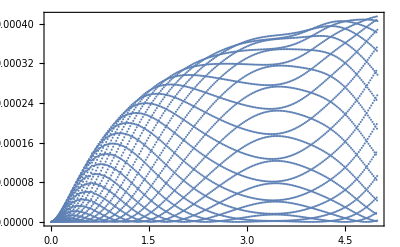
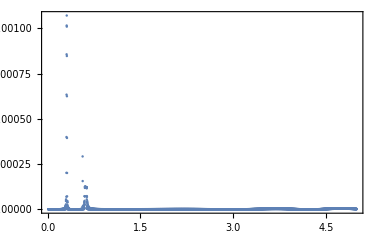
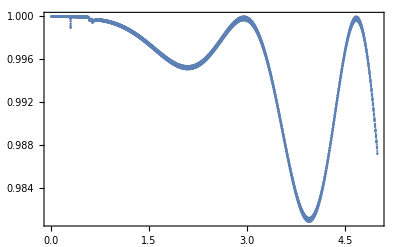
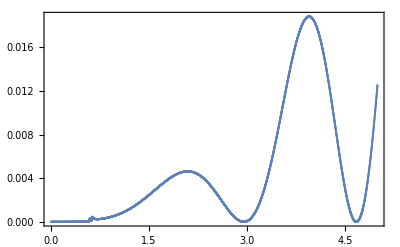

```mathematica
Module[{ii,ll=lk01},Table[ListPlot[Join[Transpose[{ll[[All,1]]}],Transpose[{Abs[ll[[All,2]][[All,ii]]]^2}],2],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
Put[lk01,NotebookDirectory[]<>"AmpPlane10"<>ToString[pp]<>".dat"];
```

```mathematica
Module[{ii,ll=lk01[[All,2]]},Table[Norm[ll[[ii]]],{ii,1, Length[ll]}]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.00001,1.00017,1.00007,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.00001,1.,1.,1.,1.,1.00001,1.00001,1.00001,1.00001,1.00001,1.,1.,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.00001,1.,1.,1.,1.,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001}

```mathematica
lk02=Module[{k0,ip=0,im=1,k0i=SetPrecision[1/100,Infinity],k0f=SetPrecision[5,Infinity],dk0=1/1000,np=SetPrecision[1/50,Infinity],tt},tt=ParallelTable[{k0,ScAmplitPlane[ip,im,k0,np,0,pp]},{k0,k0i,k0f,dk0}]];
```

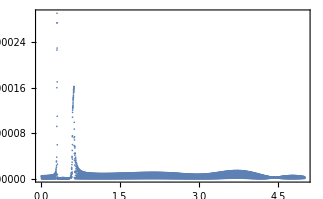
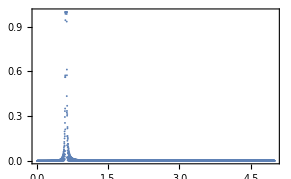
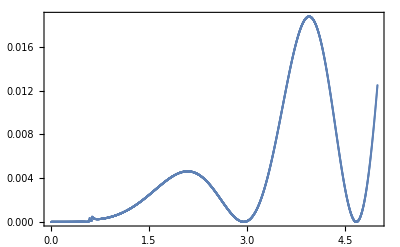
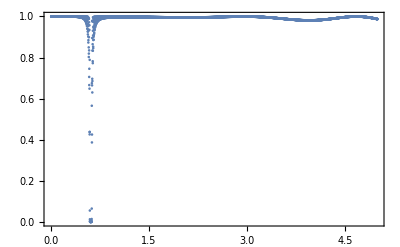

```mathematica
Module[{ii,ll=lk02},Table[ListPlot[Join[Transpose[{ll[[All,1]]}],Transpose[{Abs[ll[[All,2]][[All,ii]]]^2}],2],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
Put[lk02,NotebookDirectory[]<>"AmpPlane01"<>ToString[pp]<>".dat"];
```

```mathematica
Module[{ii,ll=lk02[[All,2]]},Table[Norm[ll[[ii]]],{ii,1, Length[ll]}]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999994,0.999974,0.999641,0.999879,0.999992,1.,0.999999,0.999996,0.999995,0.999995,0.999996,0.999998,1.,1.,0.999998,0.999996,0.999996,0.999996,0.999998,1.,1.,0.999998,0.999995,0.999994,0.999995,0.999997,1.,0.999999,0.999995,0.999992,0.99999,0.999993,0.999998,0.999999,0.99999,0.999984,0.999984,0.999995,0.999985,0.999973,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999972,0.999987,0.99999,0.999981,0.999982,0.99999,0.999999,0.999997,0.99999,0.999988,0.99999,0.999995,0.999999,0.999999,0.999996,0.999993,0.999992,0.999994,0.999998,1.,0.999999,0.999997,0.999995,0.999995,0.999996,0.999998,1.,1.,0.999998,0.999996,0.999996,0.999997,0.999998,1.,1.,0.999999,0.999997,0.999997,0.999997,0.999998,0.999999,1.,0.999999,0.999998,0.999997,0.999997,0.999998,0.999999,1.,1.,0.999999,0.999998,0.999997,0.999997,0.999998,0.999999,1.,1.,0.999998,0.999997,0.999997,0.999997,0.999998,1.,1.,0.999999,0.999996,0.999994,0.999993,0.999994,0.999996,0.999999,1.,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.00001,1.00001,1.00001,1.,0.999997,0.999992,0.999989,0.999989,0.999992,0.999996,0.999999,1.,0.999999,0.999998,0.999997,0.999997,0.999997,0.999999,1.,1.,0.999999,0.999999,0.999998,0.999998,0.999998,0.999999,1.,1.,0.999999,0.999999,0.999998,0.999998,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.,0.999997,0.999999,1.,0.999999,0.999997,0.999995,0.999995,0.999996,0.999998,1.,1.,0.999999,0.999997,0.999997,0.999997,0.999998,0.999999,1.,1.,0.999999,0.999998,0.999998,0.999998,0.999999,1.,1.,1.,0.999999,0.999998,0.999998,0.999998,0.999999,1.,1.,1.,0.999999,0.999998,0.999998,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999996,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999997,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999995,0.999995,0.999995,0.999996,0.999996,0.999996,0.999996,0.999995,0.999995,0.999995,0.999995,0.999996,0.999996,0.999996,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999996,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999994,0.999994,0.999995,0.999995,0.999995,0.999995,0.999995,0.999994,0.999994,0.999994,0.999995,0.999995,0.999995,0.999995,0.999994,0.999994,0.999994,0.999994,0.999994,0.999995,0.999995,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999995,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999993,0.999994,0.999994,0.999994,0.999994,0.999994,0.999993,0.999993,0.999993,0.999994,0.999994,0.999994,0.999994,0.999994,0.999993,0.999993,0.999993,0.999993,0.999994,0.999994,0.999994,0.999993,0.999993,0.999993,0.999993,0.999993,0.999994,0.999994,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999992,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999992,0.999992,0.999992,0.999993,0.999993,0.999993,0.999993,0.999992,0.999992,0.999992,0.999992,0.999993,0.999993,0.999993,0.999992,0.999992,0.999992,0.999992,0.999992,0.999993,0.999993,0.999993,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999993,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999993,0.999993,0.999992,0.999992,0.999992,0.999992,0.999992,0.999993,0.999993,0.999993,0.999992,0.999992,0.999992,0.999992,0.999993,0.999993,0.999993,0.999993,0.999992,0.999992,0.999992,0.999992,0.999993,0.999993,0.999993,0.999993,0.999993,0.999992,0.999992,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999994,0.999994,0.999993,0.999993,0.999993,0.999993,0.999993,0.999994,0.999994,0.999994,0.999993,0.999993,0.999993,0.999993,0.999994,0.999994,0.999994,0.999994,0.999994,0.999993,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999995,0.999994,0.999994,0.999994,0.999994,0.999994,0.999995,0.999995,0.999995,0.999995,0.999994,0.999994,0.999994,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999994,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999996,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999996,0.999996,0.999996,0.999995,0.999995,0.999995,0.999995,0.999996,0.999996,0.999996,0.999996,0.999996,0.999995,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999997,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999997,0.999997,0.999997,0.999997,0.999997,0.999996,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,1.,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,1.,0.999999,0.999999,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999995,0.999995,0.999996,0.999996,0.999996,0.999996,0.999996,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999994,0.999994,0.999994,0.999995,0.999995,0.999995,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993}

```mathematica
(*vvvvvvvv+np=1/5+vvvvvvvv*)
```

```mathematica
ll3d4=Module[{k0i=SetPrecision[0.6188,Infinity],k0f=SetPrecision[0.619,Infinity],dk0=1/100000,np=SetPrecision[1/5,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

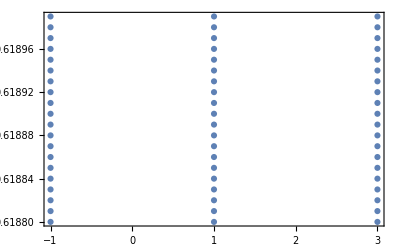

```mathematica
ListPlot[ll3d4,PlotRange->Full,Frame->True]
```

```mathematica
Chop[N[Select[ll3d4,(Re[#[[1]]]>0.9999&&Re[#[[1]]]<1.0001&&Chop[#[[1]]]∈Reals)&]]]
```

{{0.999911,0.61883},{0.999928,0.61884},{0.999944,0.61885},{0.99996,0.61886},{0.999976,0.61887},{0.999993,0.61888},{1.00001,0.61889},{1.00002,0.6189},{1.00004,0.61891},{1.00006,0.61892},{1.00007,0.61893},{1.00009,0.61894}}

```mathematica
Chop[N[Select[ll3d4,(Re[#[[2]]]>0.5915&&Re[#[[2]]]<0.5940&&Chop[#[[1]]]∈Reals)&]]]
```

{{2.95579,0.59155},{1.0054,0.59155},{0.994595,0.59155},{0.95579,0.59155},{-0.95579,0.59155},{-0.994595,0.59155},{2.95587,0.5916},{1.00464,0.5916},{0.995363,0.5916},{0.955871,0.5916},{-0.955871,0.5916},{-0.995363,0.5916},{2.95595,0.59165},{1.00372,0.59165},{0.996285,0.59165},{0.955952,0.59165},{-0.955952,0.59165},{-0.996285,0.59165},{2.95603,0.5917},{1.00247,0.5917},{0.997526,0.5917},{0.956033,0.5917},{-0.956033,0.5917},{-0.997526,0.5917},{2.95611,0.59175},{0.956113,0.59175},{-0.956113,0.59175},{2.95619,0.5918},{0.956194,0.5918},{-0.956194,0.5918},{2.95628,0.59185},{0.956275,0.59185},{-0.956275,0.59185},{2.95636,0.5919},{0.956356,0.5919},{-0.956356,0.5919},{2.95644,0.59195},{0.956437,0.59195},{-0.956437,0.59195},{2.95652,0.592},{0.956518,0.592},{-0.956518,0.592},{2.9566,0.59205},{0.956599,0.59205},{-0.956599,0.59205},{2.95668,0.5921},{0.95668,0.5921},{-0.95668,0.5921},{2.95676,0.59215},{0.95676,0.59215},{-0.95676,0.59215},{2.95684,0.5922},{0.956841,0.5922},{-0.956841,0.5922},{2.95692,0.59225},{0.956922,0.59225},{-0.956922,0.59225},{2.957,0.5923},{0.957003,0.5923},{-0.957003,0.5923},{2.95708,0.59235},{0.957084,0.59235},{-0.957084,0.59235},{2.95716,0.5924},{0.957165,0.5924},{-0.957165,0.5924},{2.95725,0.59245},{0.957246,0.59245},{-0.957246,0.59245},{2.95733,0.5925},{0.957326,0.5925},{-0.957326,0.5925},{2.95741,0.59255},{0.957407,0.59255},{-0.957407,0.59255},{2.95749,0.5926},{0.957488,0.5926},{-0.957488,0.5926},{2.95757,0.59265},{0.957569,0.59265},{-0.957569,0.59265},{2.95765,0.5927},{0.95765,0.5927},{-0.95765,0.5927},{2.95773,0.59275},{0.957731,0.59275},{-0.957731,0.59275},{2.95781,0.5928},{0.957812,0.5928},{-0.957812,0.5928},{2.95789,0.59285},{0.957893,0.59285},{-0.957893,0.59285},{2.95797,0.5929},{0.957973,0.5929},{-0.957973,0.5929},{2.95805,0.59295},{0.958054,0.59295},{-0.958054,0.59295},{2.95814,0.593},{0.958135,0.593},{-0.958135,0.593},{2.95822,0.59305},{0.958216,0.59305},{-0.958216,0.59305},{2.9583,0.5931},{0.958297,0.5931},{-0.958297,0.5931},{2.95838,0.59315},{0.958378,0.59315},{-0.958378,0.59315},{2.95846,0.5932},{0.958459,0.5932},{-0.958459,0.5932},{2.95854,0.59325},{0.958539,0.59325},{-0.958539,0.59325},{2.95862,0.5933},{0.95862,0.5933},{-0.95862,0.5933},{2.9587,0.59335},{0.958701,0.59335},{-0.958701,0.59335},{2.95878,0.5934},{0.958782,0.5934},{-0.958782,0.5934},{2.95886,0.59345},{0.958863,0.59345},{-0.958863,0.59345},{2.95894,0.5935},{0.958944,0.5935},{-0.958944,0.5935},{2.95902,0.59355},{0.959025,0.59355},{-0.959025,0.59355},{2.95911,0.5936},{0.959105,0.5936},{-0.959105,0.5936},{2.95919,0.59365},{0.959186,0.59365},{-0.959186,0.59365},{2.95927,0.5937},{0.959267,0.5937},{-0.959267,0.5937},{2.95935,0.59375},{0.959348,0.59375},{-0.959348,0.59375},{2.95943,0.5938},{0.959429,0.5938},{-0.959429,0.5938},{2.95951,0.59385},{0.95951,0.59385},{-0.95951,0.59385},{2.95959,0.5939},{0.959591,0.5939},{-0.959591,0.5939},{2.95967,0.59395},{0.959672,0.59395},{-0.959672,0.59395}}

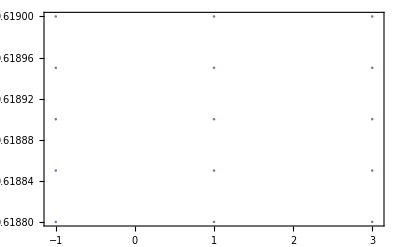

```mathematica
ListPlot[ll3d4,PlotRange->{0.6188,0.619},Frame->True]
```

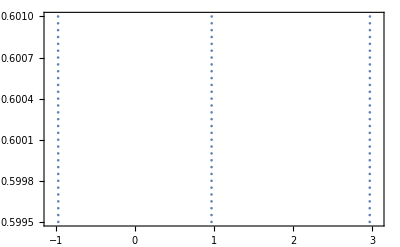

```mathematica
ListPlot[ll3d4,PlotRange->{0.5995,0.601},Frame->True]
```

```mathematica
(*^^^^^^^^^^+np=1/5+^^^^^^^^^^*)
```

```mathematica
(*vvvvvvvvvv-ищем полную щель-vvvvvvvvvv*)
```

```mathematica
ll3d=Module[{k0i=1/100,k0f=5,dk0=1/20,np=SetPrecision[0.8,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

```mathematica
ll3d=Module[{k0i=1/100,k0f=5,dk0=1/20,np=SetPrecision[0.6,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

```mathematica
ll3d1=Module[{k0i=1/100,k0f=5,dk0=1/100,np=SetPrecision[0.99,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

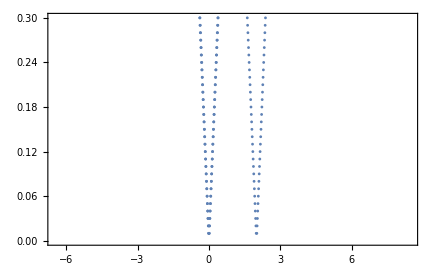
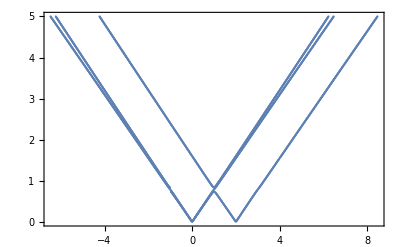

```mathematica
{ListPlot[ll3d1,PlotRange->{0,0.3},Frame->True],ListPlot[ll3d1,PlotRange->Full,Frame->True]}
```

```mathematica
ll3d2=Module[{k0i=6/10,k0f=1,dk0=1/100,np=SetPrecision[1.15,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

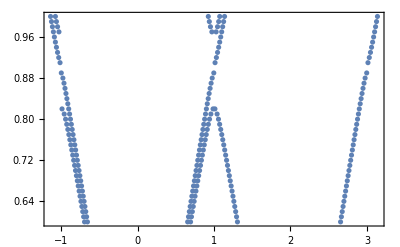

```mathematica
ListPlot[ll3d2,PlotRange->Full,Frame->True]
```

```mathematica
ll4d3=Module[{k0i=88/100,k0f=92/100,dk0=1/10000,np=SetPrecision[1.15,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

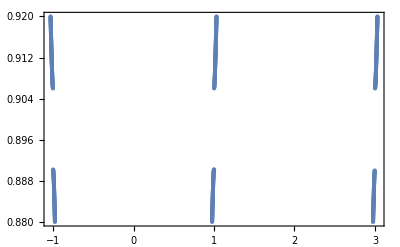

```mathematica
ListPlot[ll4d3,PlotRange->Full,Frame->True]
```

```mathematica
(*vvvvvvvvvv-np=1.1-vvvvvvvvv*)
```

```mathematica
ll3d3=Module[{k0i=84/100,k0f=88/100,dk0=1/10000,np=SetPrecision[1.1,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

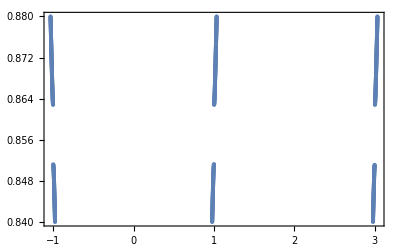

```mathematica
ListPlot[ll3d3,PlotRange->Full,Frame->True]
```

```mathematica
(*vvvv-np=0.99-vvvvv*)
```

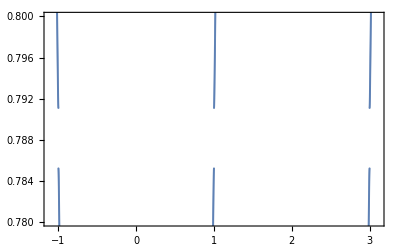

```mathematica
ListPlot[ll3d3,PlotRange->{0.78,0.8},Frame->True]
```

```mathematica
Chop[N[Select[ll3d3,(#[[2]]>0.785&&#[[2]]<0.791)&]]]
```

{{2.99881,0.7851},{1.+0.0569491 ⅈ,0.7851},{1.-0.0569491 ⅈ,0.7851},{0.998813,0.7851},{-0.998813,0.7851},{2.99961,0.7852},{1.+0.0569525 ⅈ,0.7852},{1.-0.0569525 ⅈ,0.7852},{0.999609,0.7852},{-0.999609,0.7852},{1.+0.0569557 ⅈ,0.7853},{1.-0.0569557 ⅈ,0.7853},{1.+0.0010308 ⅈ,0.7853},{1.-0.0010308 ⅈ,0.7853},{1.+0.00149539 ⅈ,0.7854},{1.-0.00149539 ⅈ,0.7854},{1.+0.0569587 ⅈ,0.7854},{1.-0.0569587 ⅈ,0.7854},{1.+0.00183526 ⅈ,0.7855},{1.-0.00183526 ⅈ,0.7855},{1.+0.0569615 ⅈ,0.7855},{1.-0.0569615 ⅈ,0.7855},{1.+0.0569641 ⅈ,0.7856},{1.-0.0569641 ⅈ,0.7856},{1.+0.00211151 ⅈ,0.7856},{1.-0.00211151 ⅈ,0.7856},{1.+0.0569666 ⅈ,0.7857},{1.-0.0569666 ⅈ,0.7857},{1.+0.00234672 ⅈ,0.7857},{1.-0.00234672 ⅈ,0.7857},{1.+0.00255226 ⅈ,0.7858},{1.-0.00255226 ⅈ,0.7858},{1.+0.0569688 ⅈ,0.7858},{1.-0.0569688 ⅈ,0.7858},{1.+0.0569708 ⅈ,0.7859},{1.-0.0569708 ⅈ,0.7859},{1.+0.00273481 ⅈ,0.7859},{1.-0.00273481 ⅈ,0.7859},{1.+0.0569726 ⅈ,0.786},{1.-0.0569726 ⅈ,0.786},{1.+0.00289874 ⅈ,0.786},{1.-0.00289874 ⅈ,0.786},{1.+0.00304703 ⅈ,0.7861},{1.-0.00304703 ⅈ,0.7861},{1.+0.0569742 ⅈ,0.7861},{1.-0.0569742 ⅈ,0.7861},{1.+0.0569756 ⅈ,0.7862},{1.-0.0569756 ⅈ,0.7862},{1.+0.00318188 ⅈ,0.7862},{1.-0.00318188 ⅈ,0.7862},{1.+0.00330493 ⅈ,0.7863},{1.-0.00330493 ⅈ,0.7863},{1.+0.0569768 ⅈ,0.7863},{1.-0.0569768 ⅈ,0.7863},{1.+0.0569778 ⅈ,0.7864},{1.-0.0569778 ⅈ,0.7864},{1.+0.00341746 ⅈ,0.7864},{1.-0.00341746 ⅈ,0.7864},{1.+0.0569787 ⅈ,0.7865},{1.-0.0569787 ⅈ,0.7865},{1.+0.00352046 ⅈ,0.7865},{1.-0.00352046 ⅈ,0.7865},{1.+0.00361475 ⅈ,0.7866},{1.-0.00361475 ⅈ,0.7866},{1.+0.0569793 ⅈ,0.7866},{1.-0.0569793 ⅈ,0.7866},{1.+0.0569797 ⅈ,0.7867},{1.-0.0569797 ⅈ,0.7867},{1.+0.00370101 ⅈ,0.7867},{1.-0.00370101 ⅈ,0.7867},{1.+0.0569799 ⅈ,0.7868},{1.-0.0569799 ⅈ,0.7868},{1.+0.00377976 ⅈ,0.7868},{1.-0.00377976 ⅈ,0.7868},{1.+0.00385148 ⅈ,0.7869},{1.-0.00385148 ⅈ,0.7869},{1.+0.0569799 ⅈ,0.7869},{1.-0.0569799 ⅈ,0.7869},{1.+0.0569797 ⅈ,0.787},{1.-0.0569797 ⅈ,0.787},{1.+0.00391655 ⅈ,0.787},{1.-0.00391655 ⅈ,0.787},{1.+0.0569793 ⅈ,0.7871},{1.-0.0569793 ⅈ,0.7871},{1.+0.00397529 ⅈ,0.7871},{1.-0.00397529 ⅈ,0.7871},{1.+0.00402798 ⅈ,0.7872},{1.-0.00402798 ⅈ,0.7872},{1.+0.0569788 ⅈ,0.7872},{1.-0.0569788 ⅈ,0.7872},{1.+0.056978 ⅈ,0.7873},{1.-0.056978 ⅈ,0.7873},{1.+0.00407485 ⅈ,0.7873},{1.-0.00407485 ⅈ,0.7873},{1.+0.056977 ⅈ,0.7874},{1.-0.056977 ⅈ,0.7874},{1.+0.0041161 ⅈ,0.7874},{1.-0.0041161 ⅈ,0.7874},{1.+0.0569758 ⅈ,0.7875},{1.-0.0569758 ⅈ,0.7875},{1.+0.0041519 ⅈ,0.7875},{1.-0.0041519 ⅈ,0.7875},{1.+0.0569744 ⅈ,0.7876},{1.-0.0569744 ⅈ,0.7876},{1.+0.00418238 ⅈ,0.7876},{1.-0.00418238 ⅈ,0.7876},{1.+0.0569729 ⅈ,0.7877},{1.-0.0569729 ⅈ,0.7877},{1.+0.00420766 ⅈ,0.7877},{1.-0.00420766 ⅈ,0.7877},{1.+0.0569711 ⅈ,0.7878},{1.-0.0569711 ⅈ,0.7878},{1.+0.00422783 ⅈ,0.7878},{1.-0.00422783 ⅈ,0.7878},{1.+0.0569691 ⅈ,0.7879},{1.-0.0569691 ⅈ,0.7879},{1.+0.00424296 ⅈ,0.7879},{1.-0.00424296 ⅈ,0.7879},{1.+0.00425311 ⅈ,0.788},{1.-0.00425311 ⅈ,0.788},{1.+0.056967 ⅈ,0.788},{1.-0.056967 ⅈ,0.788},{1.+0.0042583 ⅈ,0.7881},{1.-0.0042583 ⅈ,0.7881},{1.+0.0569646 ⅈ,0.7881},{1.-0.0569646 ⅈ,0.7881},{1.+0.00425856 ⅈ,0.7882},{1.-0.00425856 ⅈ,0.7882},{1.+0.056962 ⅈ,0.7882},{1.-0.056962 ⅈ,0.7882},{1.+0.0569593 ⅈ,0.7883},{1.-0.0569593 ⅈ,0.7883},{1.+0.00425389 ⅈ,0.7883},{1.-0.00425389 ⅈ,0.7883},{1.+0.0569563 ⅈ,0.7884},{1.-0.0569563 ⅈ,0.7884},{1.+0.00424426 ⅈ,0.7884},{1.-0.00424426 ⅈ,0.7884},{1.+0.00422965 ⅈ,0.7885},{1.-0.00422965 ⅈ,0.7885},{1.+0.0569531 ⅈ,0.7885},{1.-0.0569531 ⅈ,0.7885},{1.+0.0569498 ⅈ,0.7886},{1.-0.0569498 ⅈ,0.7886},{1.+0.00420999 ⅈ,0.7886},{1.-0.00420999 ⅈ,0.7886},{1.+0.0569462 ⅈ,0.7887},{1.-0.0569462 ⅈ,0.7887},{1.+0.00418523 ⅈ,0.7887},{1.-0.00418523 ⅈ,0.7887},{1.+0.0569425 ⅈ,0.7888},{1.-0.0569425 ⅈ,0.7888},{1.+0.00415526 ⅈ,0.7888},{1.-0.00415526 ⅈ,0.7888},{1.+0.0569385 ⅈ,0.7889},{1.-0.0569385 ⅈ,0.7889},{1.+0.00411997 ⅈ,0.7889},{1.-0.00411997 ⅈ,0.7889},{1.+0.0569344 ⅈ,0.789},{1.-0.0569344 ⅈ,0.789},{1.+0.00407922 ⅈ,0.789},{1.-0.00407922 ⅈ,0.789},{1.+0.00403284 ⅈ,0.7891},{1.-0.00403284 ⅈ,0.7891},{1.+0.05693 ⅈ,0.7891},{1.-0.05693 ⅈ,0.7891},{1.+0.0569255 ⅈ,0.7892},{1.-0.0569255 ⅈ,0.7892},{1.+0.00398065 ⅈ,0.7892},{1.-0.00398065 ⅈ,0.7892},{1.+0.0569208 ⅈ,0.7893},{1.-0.0569208 ⅈ,0.7893},{1.+0.00392239 ⅈ,0.7893},{1.-0.00392239 ⅈ,0.7893},{1.+0.00385781 ⅈ,0.7894},{1.-0.00385781 ⅈ,0.7894},{1.+0.0569158 ⅈ,0.7894},{1.-0.0569158 ⅈ,0.7894},{1.+0.00378657 ⅈ,0.7895},{1.-0.00378657 ⅈ,0.7895},{1.+0.0569107 ⅈ,0.7895},{1.-0.0569107 ⅈ,0.7895},{1.+0.00370828 ⅈ,0.7896},{1.-0.00370828 ⅈ,0.7896},{1.+0.0569053 ⅈ,0.7896},{1.-0.0569053 ⅈ,0.7896},{1.+0.0568998 ⅈ,0.7897},{1.-0.0568998 ⅈ,0.7897},{1.+0.0036225 ⅈ,0.7897},{1.-0.0036225 ⅈ,0.7897},{1.+0.00352867 ⅈ,0.7898},{1.-0.00352867 ⅈ,0.7898},{1.+0.0568941 ⅈ,0.7898},{1.-0.0568941 ⅈ,0.7898},{1.+0.00342613 ⅈ,0.7899},{1.-0.00342613 ⅈ,0.7899},{1.+0.0568882 ⅈ,0.7899},{1.-0.0568882 ⅈ,0.7899},{1.+0.056882 ⅈ,0.79},{1.-0.056882 ⅈ,0.79},{1.+0.00331407 ⅈ,0.79},{1.-0.00331407 ⅈ,0.79},{1.+0.0568757 ⅈ,0.7901},{1.-0.0568757 ⅈ,0.7901},{1.+0.00319149 ⅈ,0.7901},{1.-0.00319149 ⅈ,0.7901},{1.+0.0568692 ⅈ,0.7902},{1.-0.0568692 ⅈ,0.7902},{1.+0.00305712 ⅈ,0.7902},{1.-0.00305712 ⅈ,0.7902},{1.+0.00290933 ⅈ,0.7903},{1.-0.00290933 ⅈ,0.7903},{1.+0.0568625 ⅈ,0.7903},{1.-0.0568625 ⅈ,0.7903},{1.+0.00274595 ⅈ,0.7904},{1.-0.00274595 ⅈ,0.7904},{1.+0.0568556 ⅈ,0.7904},{1.-0.0568556 ⅈ,0.7904},{1.+0.00256399 ⅈ,0.7905},{1.-0.00256399 ⅈ,0.7905},{1.+0.0568485 ⅈ,0.7905},{1.-0.0568485 ⅈ,0.7905},{1.+0.00235917 ⅈ,0.7906},{1.-0.00235917 ⅈ,0.7906},{1.+0.0568412 ⅈ,0.7906},{1.-0.0568412 ⅈ,0.7906},{1.+0.00212489 ⅈ,0.7907},{1.-0.00212489 ⅈ,0.7907},{1.+0.0568337 ⅈ,0.7907},{1.-0.0568337 ⅈ,0.7907},{1.+0.056826 ⅈ,0.7908},{1.-0.056826 ⅈ,0.7908},{1.+0.00184997 ⅈ,0.7908},{1.-0.00184997 ⅈ,0.7908},{1.+0.00151242 ⅈ,0.7909},{1.-0.00151242 ⅈ,0.7909},{1.+0.0568181 ⅈ,0.7909},{1.-0.0568181 ⅈ,0.7909}}

```mathematica
(*^^^^^^^^^-np=0.99-^^^^^^^*)
```

```mathematica
lk03=Module[{k0,ip=1,im=0,k0i=SetPrecision[0.84,Infinity],k0f=SetPrecision[0.88,Infinity],dk0=1/10000,np=SetPrecision[1.1,Infinity],tt},tt=ParallelTable[{k0,ScAmplitPlane[ip,im,k0,np,0,pp]},{k0,k0i,k0f,dk0}]];
```

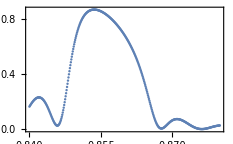
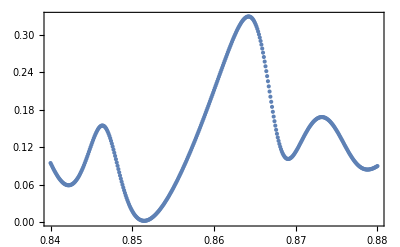
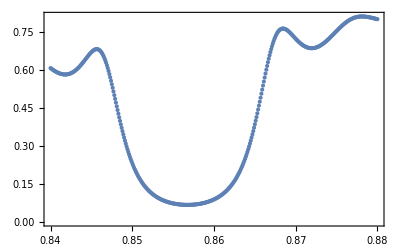
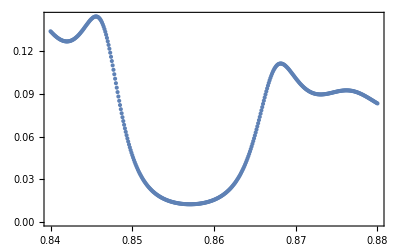

```mathematica
Module[{ii,ll=lk03},Table[ListPlot[Join[Transpose[{ll[[All,1]]}],Transpose[{Abs[ll[[All,2]][[All,ii]]]^2}],2],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
lk04=Module[{k0,ip=0,im=1,k0i=SetPrecision[0.84,Infinity],k0f=SetPrecision[0.88,Infinity],dk0=1/10000,np=SetPrecision[1.1,Infinity],tt},tt=ParallelTable[{k0,ScAmplitPlane[ip,im,k0,np,0,pp]},{k0,k0i,k0f,dk0}]];
```

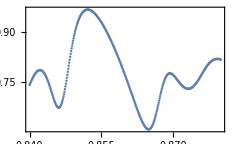
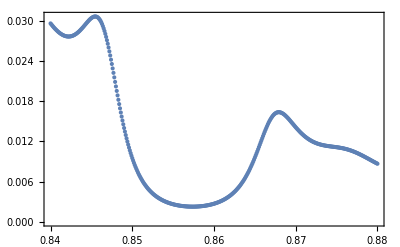
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ii,ll=lk04},Table[ListPlot[Join[Transpose[{ll[[All,1]]}],Transpose[{Abs[ll[[All,2]][[All,ii]]]^2}],2],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
(*^^^^^^^-np=1.1-^^^^^^^^^*)
```

```mathematica
(*vvvvvvvv-np=1.15-vvvvvvv*)
```

```mathematica
lk13=Module[{k0,ip=1,im=0,k0i=SetPrecision[0.88,Infinity],k0f=SetPrecision[0.92,Infinity],dk0=1/10000,np=SetPrecision[1.15,Infinity],tt},tt=ParallelTable[{k0,ScAmplitPlane[ip,im,k0,np,0,pp]},{k0,k0i,k0f,dk0}]];
```

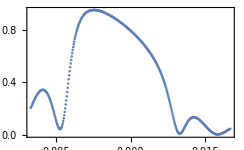
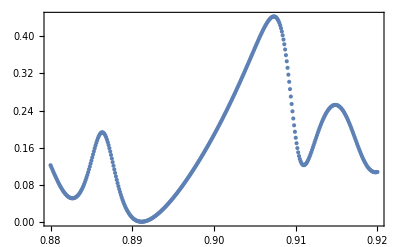
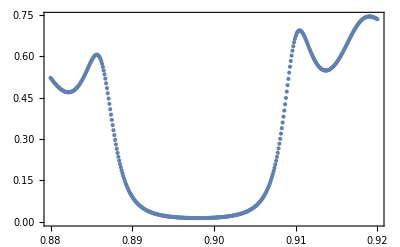
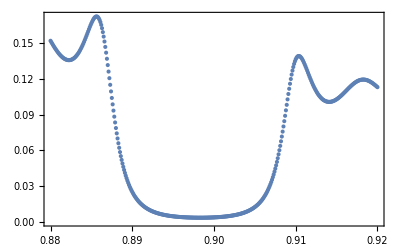

```mathematica
Module[{ii,ll=lk13},Table[ListPlot[Join[Transpose[{ll[[All,1]]}],Transpose[{Abs[ll[[All,2]][[All,ii]]]^2}],2],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
lk14=Module[{k0,ip=0,im=1,k0i=SetPrecision[0.88,Infinity],k0f=SetPrecision[0.92,Infinity],dk0=1/10000,np=SetPrecision[1.15,Infinity],tt},tt=ParallelTable[{k0,ScAmplitPlane[ip,im,k0,np,0,pp]},{k0,k0i,k0f,dk0}]];
```

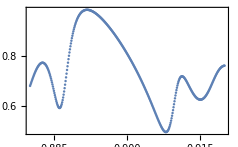
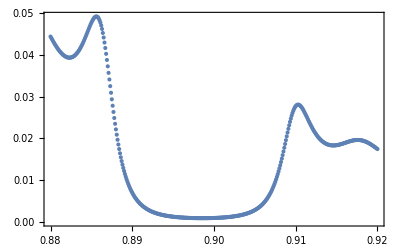
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ii,ll=lk14},Table[ListPlot[Join[Transpose[{ll[[All,1]]}],Transpose[{Abs[ll[[All,2]][[All,ii]]]^2}],2],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
(*^^^^^^^-np=1.15-^^^^^^^^^*)
```

```mathematica
(*^^^^^^^^^^-ищем полную щель-^^^^^^^^^^^*)
```

```mathematica
(*^^^^^^^-плоские фотоны-^^^^^^^*)
```

```mathematica
(*vvvvv-закрученные фотоны-vvvvvv*)
```

```mathematica
(*нужно сначала вызвать ll=ScAmplTwistTab[ip,im,m,k00,kpp,pp], а потом ScAmplTwist[m,num,ll[[3]]] для нужного значения m; num=1-4, соответствует {rp,rm,tp,tm} для заданного значения m*)
```

```mathematica
ScAmplTwistTab[1,0,1,3,3/5,pp];//RepeatedTiming
```

{1.92,Null}

```mathematica
ll1=Module[{ip=0,im=1,m=0,k00=SetPrecision[0.61,Infinity],np=1/50,kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

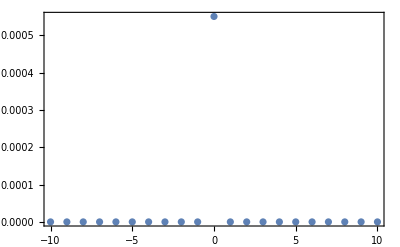
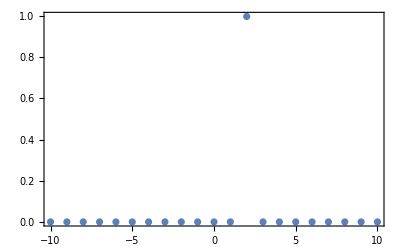
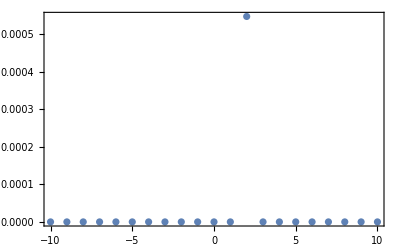
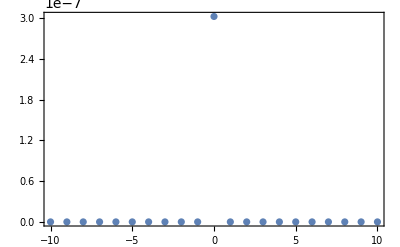

```mathematica
Module[{ll=ll1,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
ll11=Module[{ip=1,im=0,m=0,k00=SetPrecision[0.61,Infinity],np=1/50,kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

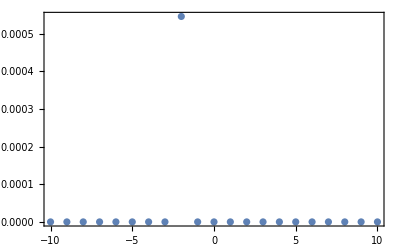
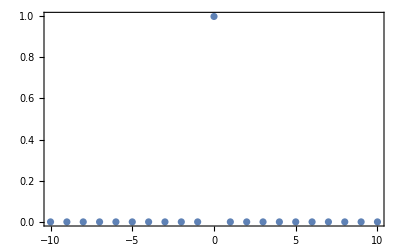
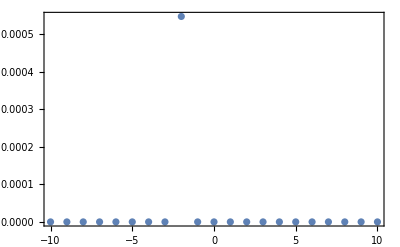
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ll=ll11,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
ll12=Module[{ip=0,im=1,m=2,k00=SetPrecision[0.61,Infinity],np=1/50,kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

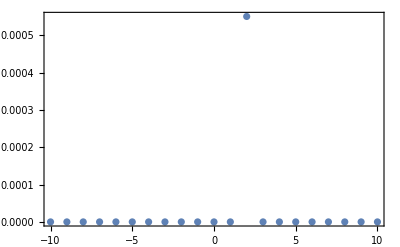
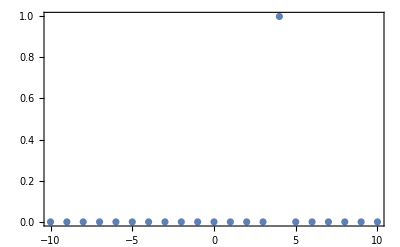
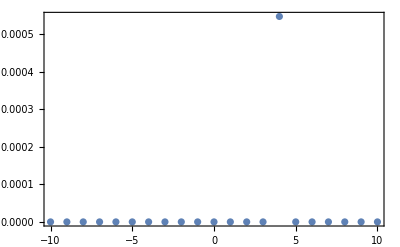
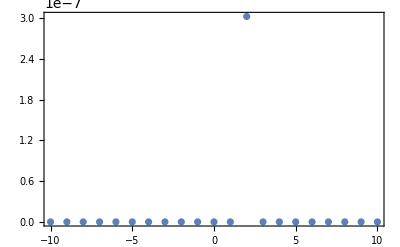

```mathematica
Module[{ll=ll12,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
ll13=Module[{ip=1,im=0,m=2,k00=SetPrecision[0.61,Infinity],np=1/50,kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

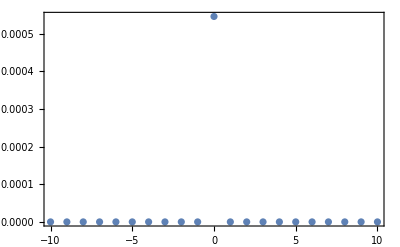
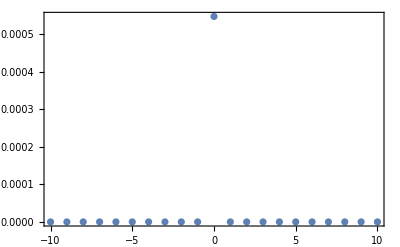
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ll=ll13,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
(*vvvvvvv+отражение на полной щели+vvvvvvvvvv*)
```

```mathematica
ll3=Module[{ip=0,im=1,m=0,k00=SetPrecision[0.853,Infinity],np=SetPrecision[1.1,Infinity],kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

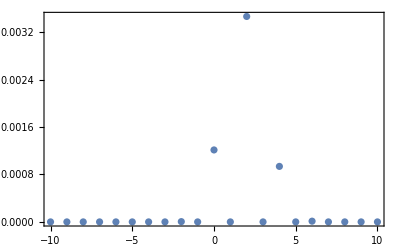
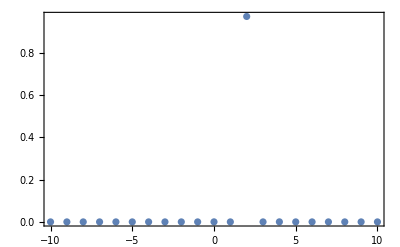
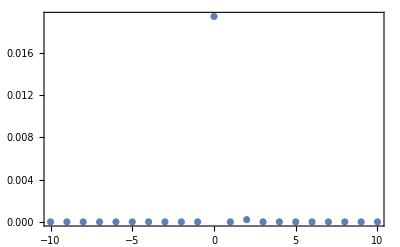
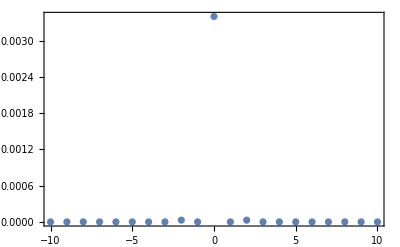

```mathematica
Module[{ll=ll3,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
ll4=Module[{ip=1,im=0,m=0,k00=SetPrecision[0.853,Infinity],np=SetPrecision[1.1,Infinity],kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

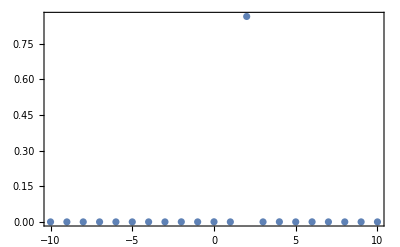
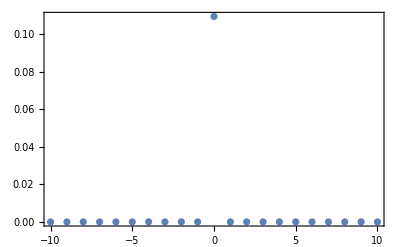
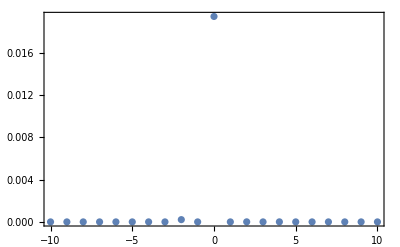
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ll=ll4,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
ll5=Module[{ip=0,im=1,m=0,k00=SetPrecision[0.892,Infinity],np=SetPrecision[1.15,Infinity],kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

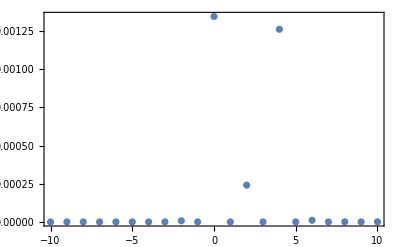
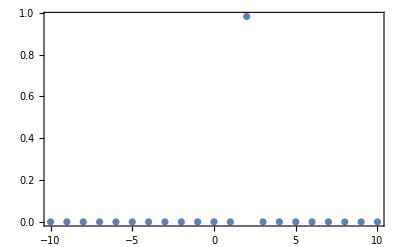
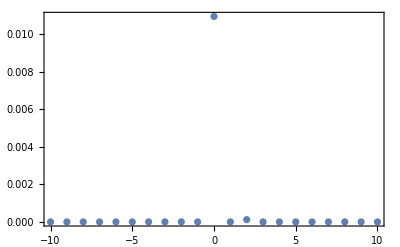
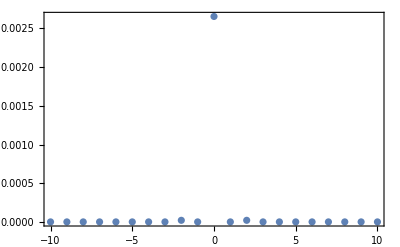

```mathematica
Module[{ll=ll5,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
ll6=Module[{ip=1,im=0,m=0,k00=SetPrecision[0.892,Infinity],np=SetPrecision[1.15,Infinity],kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

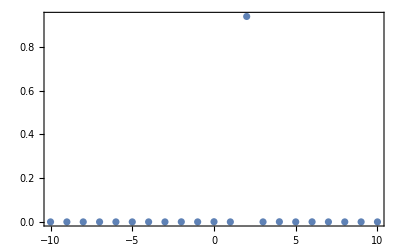
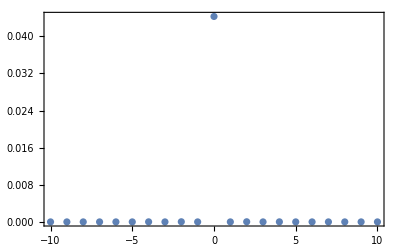
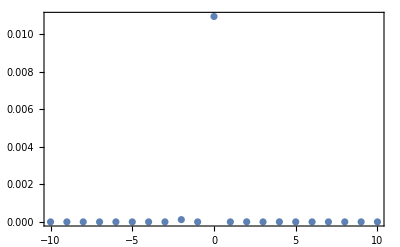
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ll=ll6,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
(*^^^^^^^^^+отражение на полной щели+^^^^^^^^^^*)
```

```mathematica
(*^^^^^-закрученные фотоны-^^^^^^*)
```

```mathematica
(*^^^^^^-примеры-^^^^^^*)
```